```mathematica
Quit[]
```

## Setup

```mathematica
restrictForHerwig=True;
```

```mathematica
FR$Parallel=False;
FRPathManuel = "D:\\Programme\\Uni\\feynrules-current\\feynrules-current";
FRPathLeonard = "/home/leonard/FeynRules/feynrules-current/";
$FeynRulesPath=SetDirectory[FRPathManuel];
<<FeynRules`
SetDirectory[NotebookDirectory[]];
LoadModel["sm.fr", "VLQ_v4.fr","eVLQ_tp2.fr","eVLQ_tp3.fr","eVLQ_S10.fr","eVLQ_S102.fr","eVLQ_S103.fr","eVLQ_S104.fr","eVLQ_S105.fr","eVLQ_S11.fr","eVLQ_S112.fr","eVLQ_S12.fr","eVLQ_Q1.fr","eVLQ_Q8.fr","eVLQ_S80.fr","eVLQ_S323.fr" ,"CHM5.fr","LRDerivative.fr"];
LoadRestriction["Massless.rst"];
(*LoadRestriction["4fns.rst"];*)
LoadRestriction["DiagonalCKM.rst"];
```

- FeynRules -

Version: 2.3.41 ( 09 December 2020).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

G. Cacciapaglia, T. Flacke, M. Kunkel, W. Porod

Model Version: 0.2

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model CHM5 loaded.

Loading restrictions from Massless.rst :  / 18

Restrictions loaded.

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

## Generate UFO

```mathematica
SetDirectory[NotebookDirectory[]];
If[restrictForHerwig,WriteUFO[ExpandIndices[LCHM5herwig],AddDecays->True],WriteUFO[ExpandIndices[LCHM5],AddDecays->True]];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

570 possible non-zero vertices have been found -> starting the computation:  / 570.

555 vertices obtained.

Flavor expansion of the vertices:  / 555

- Saved vertices in InterfaceRun[ 1 ].

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

Quantum number LeptonNumber not conserved in vertex {S323,b^-,ta}.

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

Quantum number LeptonNumber not conserved in vertex {S323,t^-,vt}.

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

General::stop: Further output of QN::NonConserv will be suppressed during this calculation.

Quantum number LeptonNumber not conserved in vertex {S323^†,ta^-,b}.

Quantum number LeptonNumber not conserved in vertex {S323^†,vt^-,t}.

Computing the squared matrix elements relevant for the 1->2 decays:

/ 466

Squared matrix elent compute in 19.5 seconds.

Decay widths computed in 0.421875 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

- Optimizing: /555 .

- Writing files.

Done!

```mathematica
CheckHermiticity[LQGIS12]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
FeynmanRules[LQGIS12]
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

3 possible non-zero vertices have been found -> starting the computation:  / 3.

3 vertices obtained.

{{{{S12,1},{S12^†,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/s_w^2-(ⅈ e^2 vev^2 η_(μ_3,μ_4))/(fpsi^2 s_w^2)},{{{A,1},{S12,2},{S12^†,3},{Z,4}},(4 ⅈ c_w e^2 η_(μ_1,μ_4))/s_w-(4 ⅈ e^2 s_w η_(μ_1,μ_4))/c_w},{{{S12,1},{S12^†,2},{Z,3},{Z,4}},-4 ⅈ e^2 η_(μ_3,μ_4)+(2 ⅈ c_w^2 e^2 η_(μ_3,μ_4))/s_w^2+(2 ⅈ e^2 s_w^2 η_(μ_3,μ_4))/c_w^2}}

```mathematica
FRvertices=FeynmanRules[LCHM5herwig];
decays=ComputeWidths[FRvertices];
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

333 possible non-zero vertices have been found -> starting the computation:  / 333.

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

Quantum number LeptonNumber not conserved in vertex {b^-,ta,S323}.

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

Quantum number LeptonNumber not conserved in vertex {t^-,vt,S323}.

QN::NonConserv: Warning: non quantum number conserving vertex encountered!

General::stop: Further output of QN::NonConserv will be suppressed during this calculation.

Quantum number LeptonNumber not conserved in vertex {ta^-,b,S323^†}.

Quantum number LeptonNumber not conserved in vertex {vt^-,t,S323^†}.

328 vertices obtained.

Flavor expansion of the vertices:  / 328

Computing the squared matrix elements relevant for the 1->2 decays:

/ 466

Decay::Overwrite: Warning: Previous results will be overwritten.

```mathematica
(*S11 + S112*)
replacements={MW->80.379,MZ->91.1876,sw->Sqrt[0.2229],cw->Sqrt[1-0.2229]};
wS11WA = PartialWidth[{S11,W,A},decays];
wS11WZ = PartialWidth[{S11,W,Z},decays];
Print["{",
InputForm[(wS11WA/(wS11WA+wS11WZ)//FullSimplify)]/.replacements,",",
InputForm[(wS11WZ/(wS11WA+wS11WZ)//FullSimplify)]/.replacements,"}"]
```

{(4.486316733961418*(-80.379 + MS11)^3*(80.379 + MS11)^3)/(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2) + 4.486316733961418*(-6460.783641000001 + MS11^2)^3),(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2))/(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2) + 4.486316733961418*(-6460.783641000001 + MS11^2)^3)}

```mathematica
{(4.486316733961418*(-80.379 + MS11)^3*(80.379 + MS11)^3)/(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2) + 4.486316733961418*(-6460.783641000001 + MS11^2)^3),(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2))/(1.2868356710848023*((-171.5666 + MS11)*(-10.808599999999998 + MS11)*(10.808599999999998 + MS11)*(171.5666 + MS11))^(3/2) + 4.486316733961418*(-6460.783641000001 + MS11^2)^3)}
```

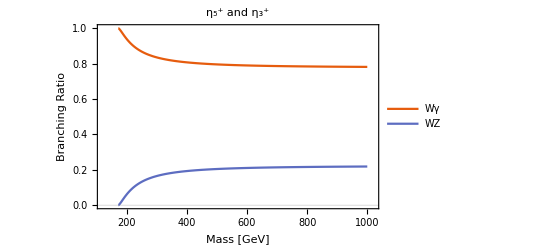

```mathematica
Plot[{(4.486316733961418 (-80.379+MS11)^3 (80.379+MS11)^3)/(1.2868356710848023 ((-171.5666+MS11) (-10.808599999999998+MS11) (10.808599999999998+MS11) (171.5666+MS11))^(3/2)+4.486316733961418 (-6460.783641000001+MS11^2)^3),(1.2868356710848023 ((-171.5666+MS11) (-10.808599999999998+MS11) (10.808599999999998+MS11) (171.5666+MS11))^(3/2))/(1.2868356710848023 ((-171.5666+MS11) (-10.808599999999998+MS11) (10.808599999999998+MS11) (171.5666+MS11))^(3/2)+4.486316733961418 (-6460.783641000001+MS11^2)^3)},{MS11,100,1000},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Wγ","WZ"},LegendMarkerSize->15],{Left,Center}],FrameTicksStyle->Larger,LabelStyle->Larger,PlotLabel->"η_5^+ and η_3^+",PlotRange->{{120,1020},{0,1}},FrameLabel->{"Mass [GeV]","Branching Ratio"}]
```

```mathematica
(*S10*)
wS10AA = PartialWidth[{S10,A,A},decays];
wS10AZ = PartialWidth[{S10,A,Z},decays];
wS10ZZ = PartialWidth[{S10,Z,Z},decays];
wS10WW = PartialWidth[{S10,W,Wbar},decays];
Print["{",
InputForm[(wS10AA/(wS10AA+wS10AZ+wS10ZZ+wS10WW)//FullSimplify)]/.replacements,",",
InputForm[(wS10AZ/(wS10AA+wS10AZ+wS10ZZ+wS10WW)//FullSimplify)]/.replacements,",",InputForm[(wS10ZZ/(wS10AA+wS10AZ+wS10ZZ+wS10WW)//FullSimplify)]/.replacements,",",InputForm[(wS10WW/(wS10AA+wS10AZ+wS10ZZ+wS10WW)//FullSimplify)]/.replacements,"}"]
```

{(64*MS10^6)/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(56.74087696147905*(-91.1876 + MS10)^3*(91.1876 + MS10)^3)/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(227.7868651472973*(-182.3752 + MS10)*MS10^2*(182.3752 + MS10)*Sqrt[-33260.713575040005*MS10^2 + MS10^4])/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2))/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2))}

```mathematica
Plot[{(64*MS10^6)/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(56.74087696147905*(-91.1876 + MS10)^3*(91.1876 + MS10)^3)/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(227.7868651472973*(-182.3752 + MS10)*MS10^2*(182.3752 + MS10)*Sqrt[-33260.713575040005*MS10^2 + MS10^4])/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2)),(644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2))/(64*MS10^6 + 56.74087696147905*(-8315.178393760001 + MS10^2)^3 + 227.7868651472973*MS10^2*(-33260.713575040005 + MS10^2)*Sqrt[-33260.713575040005*MS10^2 + MS10^4] + 644.0652107975119*(-25843.134564000004*MS10^2 + MS10^4)^(3/2))},{MS10,100,1000},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"γγ","γZ","ZZ","WW"},LegendMarkerSize->15],{Left,Center}],FrameTicksStyle->Larger,LabelStyle->Larger,PlotLabel->"η",PlotRange->{{120,1000},{0,0.7}},FrameLabel->{"Mass [GeV]","Branching Ratio"}]
```

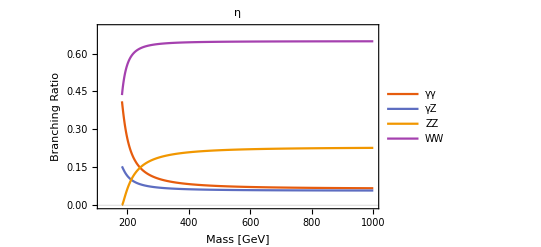

```mathematica
(*S102*)
wS102AA = PartialWidth[{S102,A,A},decays];
wS102AZ = PartialWidth[{S102,A,Z},decays];
wS102ZZ = PartialWidth[{S102,Z,Z},decays];
Print["{",
InputForm[(wS102AA/(wS102AA+wS102AZ+wS102ZZ)//FullSimplify)]/.replacements,",",
InputForm[(wS102AZ/(wS102AA+wS102AZ+wS102ZZ)//FullSimplify)]/.replacements,",",InputForm[(wS102ZZ/(wS102AA+wS102AZ+wS102ZZ)//FullSimplify)]/.replacements,"}"]
```

{(1.38572472*MS102^6)/(-7.063301541415026*^11 + 2.614275280000001*MS102^6 + 8315.178393760001*MS102^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS102^2 + MS102^4]) + MS102^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS102^2 + MS102^4])),(1.2285505600000002*(-8315.178393760001 + MS102^2)^3)/(-7.063301541415026*^11 + 2.614275280000001*MS102^6 + 8315.178393760001*MS102^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS102^2 + MS102^4]) + MS102^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS102^2 + MS102^4])),(8*(-33260.713575040005*MS102^2 + MS102^4)^(3/2))/(8*MS102^6 + 7.092609620184882*(-8315.178393760001 + MS102^2)^3 + 8*(-33260.713575040005*MS102^2 + MS102^4)^(3/2))}

```mathematica
Plot[{(1.38572472*MS102^6)/(-7.063301541415026*^11 + 2.614275280000001*MS102^6 + 8315.178393760001*MS102^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS102^2 + MS102^4]) + MS102^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS102^2 + MS102^4])),(1.2285505600000002*(-8315.178393760001 + MS102^2)^3)/(-7.063301541415026*^11 + 2.614275280000001*MS102^6 + 8315.178393760001*MS102^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS102^2 + MS102^4]) + MS102^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS102^2 + MS102^4])),(8*(-33260.713575040005*MS102^2 + MS102^4)^(3/2))/(8*MS102^6 + 7.092609620184882*(-8315.178393760001 + MS102^2)^3 + 8*(-33260.713575040005*MS102^2 + MS102^4)^(3/2))},{MS102,100,1000},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"γγ","γZ","ZZ"},LegendMarkerSize->15],{Left,Center}],FrameTicksStyle->Larger,LabelStyle->Larger,PlotLabel->"η_1^0",PlotRange->{{120,1000},{0,0.8}},FrameLabel->{"Mass [GeV]","Branching Ratio"}]
```

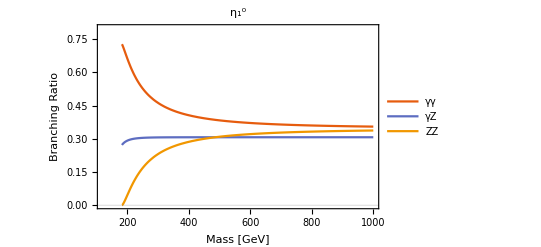

```mathematica
(*S104*)
wS104AA = PartialWidth[{S104,A,A},decays];
wS104AZ = PartialWidth[{S104,A,Z},decays];
wS104ZZ = PartialWidth[{S104,Z,Z},decays];
Print["{",
InputForm[(wS104AA/(wS104AA+wS104AZ+wS104ZZ)//FullSimplify)]/.replacements,",",
InputForm[(wS104AZ/(wS104AA+wS104AZ+wS104ZZ)//FullSimplify)]/.replacements,",",InputForm[(wS104ZZ/(wS104AA+wS104AZ+wS104ZZ)//FullSimplify)]/.replacements,"}"]
```

{(1.38572472*MS104^6)/(-7.063301541415026*^11 + 2.614275280000001*MS104^6 + 8315.178393760001*MS104^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS104^2 + MS104^4]) + MS104^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS104^2 + MS104^4])),(1.2285505600000002*(-8315.178393760001 + MS104^2)^3)/(-7.063301541415026*^11 + 2.614275280000001*MS104^6 + 8315.178393760001*MS104^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS104^2 + MS104^4]) + MS104^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS104^2 + MS104^4])),(8*(-33260.713575040005*MS104^2 + MS104^4)^(3/2))/(8*MS104^6 + 7.092609620184882*(-8315.178393760001 + MS104^2)^3 + 8*(-33260.713575040005*MS104^2 + MS104^4)^(3/2))}

```mathematica
Plot[{(1.38572472*MS104^6)/(-7.063301541415026*^11 + 2.614275280000001*MS104^6 + 8315.178393760001*MS104^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS104^2 + MS104^4]) + MS104^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS104^2 + MS104^4])),(1.2285505600000002*(-8315.178393760001 + MS104^2)^3)/(-7.063301541415026*^11 + 2.614275280000001*MS104^6 + 8315.178393760001*MS104^2*(30646.851216461255 - 5.54289888*Sqrt[-33260.713575040005*MS104^2 + MS104^4]) + MS104^4*(-30646.851216461255 + 1.38572472*Sqrt[-33260.713575040005*MS104^2 + MS104^4])),(8*(-33260.713575040005*MS104^2 + MS104^4)^(3/2))/(8*MS104^6 + 7.092609620184882*(-8315.178393760001 + MS104^2)^3 + 8*(-33260.713575040005*MS104^2 + MS104^4)^(3/2))},{MS104,100,1000},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"γγ","γZ","ZZ"},LegendMarkerSize->15],{Left,Center}],FrameTicksStyle->Larger,LabelStyle->Larger,PlotLabel->"η_5^0",PlotRange->{{120,1000},{0,0.8}},FrameLabel->{"Mass [GeV]","Branching Ratio"}]
```